Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

3.  Inverse. If w = f[z] is any transformation that has an inverse, prove the fact that f and its inverse have the same fixed points.

```mathematica
Clear["Global`*"]
```

This may be a pud proof, but... I assume that w=f[x] has at least one fixed point. However many it has, consider an arbitrary fixed point z_1 in z-plane which gets mapped to w-plane by w=f[z], to a point called w_1.And the inverse of w,  w^-1, a mapping in its own right, takes the point w_1and operates on it to map it to the z-plane, to the exact point where it originated, that being the inverse function’s function. Now w_1 =z_1 because z_1 is a fixed point for w. By observing w^-1 as it maps w_1 to z_1, with which it is equal, I can see that w_1 is a fixed point for w^-1.  The establishment of the fixed point in w^-1 is separate and independent of the establishment of z_1 as a fixed point for w, yet, as if I didn’t already know, I can look at z_1 and w_1 and see that they are equal. Therefore the mapping functions have a fixed point that is the same, and if they have this arbitrary one, they share all in common.

5. Derive the mapping in Example 2 from numbered line (2) on p. 746.

```mathematica
Clear["Global`*"]
```

```mathematica
Subscript[z, 1]=0
```

0

```mathematica
Subscript[z, 2]=1
```

1

Mathematica cannot swallow ∞ assigned to a variable in this context. For now, it needs to be symbolic, as below. (Note: the w-z assignment formula has its own means of dealing with occurrences of ∞, but with Mathematica I can take care of it a different way.)

```mathematica
Subscript[z, 3]=a
```

a

```mathematica
Subscript[w, 1]=-1
```

-1

```mathematica
Subscript[w, 2]=-ⅈ
```

-ⅈ

```mathematica
Subscript[w, 3]=1
```

1

```mathematica
Solve[(w-Subscript[w, 1])/(w-Subscript[w, 3])((Subscript[w, 2]-Subscript[w, 3])/(Subscript[w, 2]-Subscript[w, 1]))==(z-Subscript[z, 1])/(z-Subscript[z, 3])((Subscript[z, 2]-Subscript[z, 3])/(Subscript[z, 2]-Subscript[z, 1])),{w,z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{w→(-ⅈ a-(1-ⅈ) z+a z)/(ⅈ a-(1+ⅈ) z+a z)}}

```mathematica
Limit[(-ⅈ a-(1-ⅈ) z+a z)/(ⅈ a-(1+ⅈ) z+a z),a->∞]
```

(-ⅈ+z)/(ⅈ+z)

The expression in the green cell above matches the answer to example 2 on p. 748.

8 - 16 LFTs from three points and images
Find the LFT that maps the given three points onto the three given points in the respective order.

9.  1,ⅈ,-1onto ⅈ,-1,-ⅈ

```mathematica
Clear["Global`*"]
```

```mathematica
Subscript[z, 1]=1
```

1

```mathematica
Subscript[z, 2]=ⅈ
```

ⅈ

```mathematica
Subscript[z, 3]=-1
```

-1

```mathematica
Subscript[w, 1]=ⅈ
```

ⅈ

```mathematica
Subscript[w, 2]=-1
```

-1

```mathematica
Subscript[w, 3]=-ⅈ
```

-ⅈ

```mathematica
Solve[(w-Subscript[w, 1])/(w-Subscript[w, 3])((Subscript[w, 2]-Subscript[w, 3])/(Subscript[w, 2]-Subscript[w, 1]))==(z-Subscript[z, 1])/(z-Subscript[z, 3])((Subscript[z, 2]-Subscript[z, 3])/(Subscript[z, 2]-Subscript[z, 1])),{w}]
```

{{w→ⅈ z}}

11.  - 1, 0, 1 onto - ⅈ, -1, ⅈ

```mathematica
Clear["Global`*"]
```

```mathematica
Subscript[z, 1]=-1
```

-1

```mathematica
Subscript[z, 2]=0
```

0

```mathematica
Subscript[z, 3]=1
```

1

```mathematica
Subscript[w, 1]=-ⅈ
```

-ⅈ

```mathematica
Subscript[w, 2]=-1
```

-1

```mathematica
Subscript[w, 3]=ⅈ
```

ⅈ

```mathematica
Solve[(w-Subscript[w, 1])/(w-Subscript[w, 3])((Subscript[w, 2]-Subscript[w, 3])/(Subscript[w, 2]-Subscript[w, 1]))==(z-Subscript[z, 1])/(z-Subscript[z, 3])((Subscript[z, 2]-Subscript[z, 3])/(Subscript[z, 2]-Subscript[z, 1])),{w}]
```

{{w→(ⅈ+z)/(-ⅈ+z)}}

13.  0, 1, ∞ onto ∞, 1, 0

```mathematica
Clear["Global`*"]
```

```mathematica
Subscript[z, 1]=0
```

0

```mathematica
Subscript[z, 2]=1
```

1

```mathematica
Subscript[z, 3]=a
```

a

```mathematica
Subscript[w, 1]=a
```

a

```mathematica
Subscript[w, 2]=1
```

1

```mathematica
Subscript[w, 3]=0
```

0

```mathematica
Solve[(w-Subscript[w, 1])/(w-Subscript[w, 3])((Subscript[w, 2]-Subscript[w, 3])/(Subscript[w, 2]-Subscript[w, 1]))==(z-Subscript[z, 1])/(z-Subscript[z, 3])((Subscript[z, 2]-Subscript[z, 3])/(Subscript[z, 2]-Subscript[z, 1])),{w}]
```

{{w→(a-z)/(1-2 z+a z)}}

```mathematica
Limit[(a-z)/(1-2 z+a z),a->∞]
```

1/z

15.  1, ⅈ, 2 onto 0, -ⅈ-1, -1/2

```mathematica
Clear["Global`*"]
```

```mathematica
Subscript[z, 1]=1
```

1

```mathematica
Subscript[z, 2]=ⅈ
```

ⅈ

```mathematica
Subscript[z, 3]=2
```

2

```mathematica
Subscript[w, 1]=0
```

0

```mathematica
Subscript[w, 2]=-ⅈ-1
```

-1-ⅈ

```mathematica
Subscript[w, 3]=-1/2
```

-1/2

```mathematica
Solve[(w-Subscript[w, 1])/(w-Subscript[w, 3])((Subscript[w, 2]-Subscript[w, 3])/(Subscript[w, 2]-Subscript[w, 1]))==(z-Subscript[z, 1])/(z-Subscript[z, 3])((Subscript[z, 2]-Subscript[z, 3])/(Subscript[z, 2]-Subscript[z, 1])),{w}]
```

{{w→(1-z)/z}}

17. Find an LFT that maps |z|≤1 onto |w|≤1 so that z=ⅈ/2 is mapped onto w=0. Sketch the images of the lines x=const and y=const.

```mathematica
Clear["Global`*"]
```

Numbered line (3) on p. 749 is part of an example that works this problem out for me, except it is left in general form, the z-plane point z_0 being mapped to the origin of the w-plane, while the z-unit-circle is mapped to the w-unit-circle.

w=(z-z_0)/(c z -1), c=z_0*, Abs[z_0]<1

One caveat here is that of the need to tailor c, the conjugate of z_0, to the specific z_0 chosen.

```mathematica
Subscript[z, 0]=ⅈ/2
```

ⅈ/2

```mathematica
zcon=Subscript[z, 0]*
```

-ⅈ/2

```mathematica
w[z_]=(z-ⅈ/2)/(zcon z-1)
```

(-ⅈ/2+z)/(-1-(ⅈ z)/2)

```mathematica
Simplify[%]
```

(1+2 ⅈ z)/(-2 ⅈ+z)

The cell below demonstrates that the green cell agrees with the text answer in content.

```mathematica
PossibleZeroQ[(1+2 ⅈ z)/(-2 ⅈ+z)-(2 z-ⅈ)/(-(ⅈ z+2))]
```

True

The transformation w maps the point z=0+ⅈ/2 on the z-plane to w=0+0ⅈ on the w-plane. In the z-plane plot its location is consistent with the vertical axis location, and in the w-plane plot it is shown correctly.

As for the original and transformed circles, and constant lines, the mapping w is allowed to do its work directly wherever possible.  Two intersecting test lines demonstrate that intersection angles are preserved under conformal mapping.

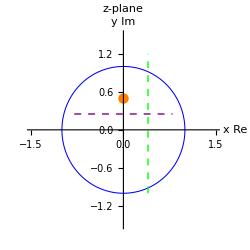
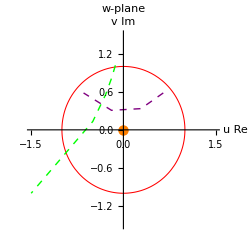

```mathematica
Row[{ParametricPlot[{Re[( ⅇ^(ⅈ t)+0)],Im[( ⅇ^(ⅈ t))]},{t,0,2π},ImageSize->250,PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->Automatic,PlotStyle->{Blue, Thickness[0.003]},Epilog->{{Orange,PointSize[0.03],Point[{0,1/2}]},{Dashed,Green,Line[{{0.4,-1},{0.4,1.2}}]},{Dashed,Purple,Line[{{-0.8,0.25},{0.8,0.25}}]}},AxesLabel->{"x Re","y Im"},PlotLabel->Style[Framed[  "  z-plane "],10,Blue,Background->White]],ParametricPlot[{Re[( (1+2 ⅈ ⅇ^(ⅈ t))/(-2 ⅈ+ⅇ^(ⅈ t)))],Im[( (1+2 ⅈ ⅇ^(ⅈ t))/(-2 ⅈ+ⅇ^(ⅈ t)))]},{t,0,2π},ImageSize->250,PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->Automatic,PlotStyle->{Red, Thickness[0.003]},Epilog->{{Orange,PointSize[0.03],Point[{Re[(1+2 ⅈ z)/(-2 ⅈ+z)/.z->(0+ⅈ/2)],Im[(1+2 ⅈ z)/(-2 ⅈ+z)/.z->(0+ⅈ/2)]}]},{Dashed,Green,Line[{{Re[(1+2 ⅈ z)/(-2 ⅈ+z)/.z->(0.4-ⅈ)],Im[(1+2 ⅈ z)/(-2 ⅈ+z)/.z->(0.4-ⅈ)]},{Re[(1+2 ⅈ z)/(-2 ⅈ+z)/.z->(0.4-0.5ⅈ)],Im[(1+2 ⅈ z)/(-2 ⅈ+z)/.z->(0.4-0.5ⅈ)]},{Re[(1+2 ⅈ z)/(-2 ⅈ+z)/.z->(0.4-0ⅈ)],Im[(1+2 ⅈ z)/(-2 ⅈ+z)/.z->(0.4-0ⅈ)]},{Re[(1+2 ⅈ z)/(-2 ⅈ+z)/.z->(0.4+0.5ⅈ)],Im[(1+2 ⅈ z)/(-2 ⅈ+z)/.z->(0.4+0.5ⅈ)]},{Re[(1+2 ⅈ z)/(-2 ⅈ+z)/.z->(0.4+1.2ⅈ)],Im[(1+2 ⅈ z)/(-2 ⅈ+z)/.z->(0.4+1.2ⅈ)]}}]},{Dashed,Purple,Line[{{Re[(1+2 ⅈ z)/(-2 ⅈ+z)/.z->(-0.8+0.25ⅈ)],Im[(1+2 ⅈ z)/(-2 ⅈ+z)/.z->(-0.8+0.25ⅈ)]},{Re[(1+2 ⅈ z)/(-2 ⅈ+z)/.z->(-0.3+0.25ⅈ)],Im[(1+2 ⅈ z)/(-2 ⅈ+z)/.z->(-0.3+0.25ⅈ)]},{Re[(1+2 ⅈ z)/(-2 ⅈ+z)/.z->(0.2+0.25ⅈ)],Im[(1+2 ⅈ z)/(-2 ⅈ+z)/.z->(0.2+0.25ⅈ)]},{Re[(1+2 ⅈ z)/(-2 ⅈ+z)/.z->0.8+0.25ⅈ],Im[(1+2 ⅈ z)/(-2 ⅈ+z)/.z->0.8+0.25
ⅈ]}}]}},AxesLabel->{"u Re","v Im"},PlotLabel->Style[Framed[  "  w-plane "],10,Red,Background->White]]}]
```

19. Find an analytic function w=f[z] that maps the region 0≤Arg[z]≤π/4 onto the unit disk |w|≤1.

```mathematica
Clear["Global`*"]
```

A hint from s.m. points me to example 2 on p. 739. This explains how to map a wedge sector onto an upper half plane. The upshot is that a wedge sector 0 ≤  ≤ π/n can be mapped to the upper half plane v ≥ 0 using the transform z^n. In this problem I have a sector from 0 to π/4 , so n =4. As far as the r value goes, it can be anything above about 2, but it can’t be ∞. I assume that setting it at 4 arbitrarily will not undermine the argument that the demo is general.

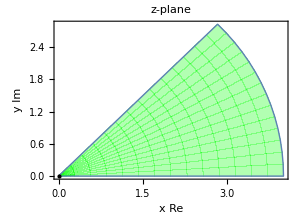
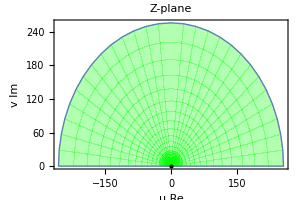

```mathematica
Row[{ParametricPlot[{Re[r( ⅇ^(ⅈ t))],Im[(r ⅇ^(ⅈ t))]},{t,0,π/4},{r,0,4},ImageSize->300,PlotStyle->{Green,Thickness[0.004]},Epilog->{{Point[{0,0}]}},Axes->True,AxesLabel->{"x Re","y Im"},PlotRange->{{-1,5},{3,-2.5}},PlotLabel->Style[Framed[  "  z-plane "],10,Blue,Background->White]] ,ParametricPlot[{Re[(r ⅇ^(ⅈ t))^4],Im[(r ⅇ^(ⅈ t))^4]},{t,0,π/4},{r,0,4},ImageSize->300,PlotStyle->{Green,Thickness[0.004]},Epilog->{{Point[{Re[(r ⅇ^(ⅈ t))^4/.{t->0,r->0}],Im[(r ⅇ^(ⅈ t))^4/.{t->0,r->0}]}]}},AxesLabel->{"u Re","v Im"},PlotRange->{{-5,5},{3,-3}},PlotLabel->Style[Framed[  "  Z-plane "],10,Red,Background->White]] }]
```

As the plot windows above show, the mapping scheme is successful so far. The next phase is to figure out how to map the upper half plane to a unit circle on the w-plane. The strategy used by the s.m., which I will follow, will be to use the mapping formula advanced in problem 5 and following. To do this I need to pick three points on Z-plane and three others on w-plane and then calculate the expression to do it. As suggesed by s.m., I choose -1, 0, and 1 on the u axis of Z-plane, and intend to map them to (-1, -ⅈ, and 1), on the unit circle, in the w-plane.

```mathematica
Subscript[Z, 1]=-1
```

-1

```mathematica
Subscript[Z, 2]=0
```

0

```mathematica
Subscript[Z, 3]=1
```

1

```mathematica
Subscript[w, 1]=-1
```

-1

```mathematica
Subscript[w, 2]=-ⅈ
```

-ⅈ

```mathematica
Subscript[w, 3]=1
```

1

```mathematica
exp1=Simplify[Solve[(w-Subscript[w, 1])/(w-Subscript[w, 3])((Subscript[w, 2]-Subscript[w, 3])/(Subscript[w, 2]-Subscript[w, 1]))==(Z-Subscript[Z, 1])/(Z-Subscript[Z, 3])((Subscript[Z, 2]-Subscript[Z, 3])/(Subscript[Z, 2]-Subscript[Z, 1])),{w}]]
```

{{w→(1+ⅈ Z)/(ⅈ+Z)}}

To re-wind this mapping back to the original sector, I make a substitution,

```mathematica
exp2=exp1/.Z->z^4
```

{{w→(1+ⅈ z^4)/(ⅈ+z^4)}}

Since this does not look exactly like the text answer, I check its equivalence, then confer the green.

```mathematica
PossibleZeroQ[(1+ⅈ z^4)/(ⅈ+z^4)-(z^4-ⅈ)/(-ⅈ z^4+1)]
```

True

Time to set up the final mapping transit, taking points from the z-plane pie sector to the w-plane unit circle.

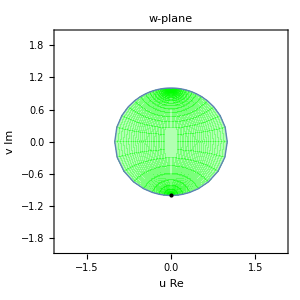

```mathematica
ParametricPlot[{Re[((r ⅇ^(ⅈ t))^4-ⅈ)/(-ⅈ(r ⅇ^(ⅈ t))^4+1)],Im[((r ⅇ^(ⅈ t))^4-ⅈ)/(-ⅈ(r ⅇ^(ⅈ t))^4+1)]},{t,0,π/4},{r,0,4},ImageSize->300,PlotStyle->{Green,Thickness[0.004]},Epilog->{{Point[{Re[((r ⅇ^(ⅈ t))^4-ⅈ)/(-ⅈ(r ⅇ^(ⅈ t))^4+1)/.{t->0,r->0}],Im[((r ⅇ^(ⅈ t))^4-ⅈ)/(-ⅈ(r ⅇ^(ⅈ t))^4+1)/.{t->0,r->0}]}]}},AxesLabel->{"u Re","v Im"},PlotRange->{{-2,2},{-2,2}},PlotLabel->Style[Framed[  "  w-plane "],10,Red,Background->White]]
```

The origin point of the z-plane ends up at the bottom of the unit circle in the w-plane.